Описание задачи
функция: t_i(x_i,c_i) = t_i^0(1 + 0.15* [x_i/c_i]^4)   i = OverBar[1 ,n], t_i^0 > 0
оптимизационная задача верхнего уровня:  min_c∑_(i=1)^n t_(i (x_i,c_i))x_i 
ограничения: на c: ∑_(i=1)^n c_i< C, c_i≥ 0
оптимизационная задача нижнего уровня: x_i = arg min_x∑_(i=1)^n ∫_0^x_i t_i(u,c_i)ⅆu
ограничения: на x: ∑_(i=1)^n x_i= F, x_i≥ 0
C > 0, F > 0
Задание: разработать эволюционный алгоритм, решающий задачу двухуровневой оптимизации для разных наборов значений
C > 0, F > 0,  n и   t_i^0 > 0,  i = OverBar[1 ,n]

```mathematica
(* Исходные данные *)
n = 3; m =50;С = 100; F = 100; t0 = 1; iterrationAmount = 500; w1 = 0.1; r = 2;
μ = 3; λ = 2; p = 2; crossoverProbability = 0.5; mutationProbability = 0.1;
variableNumberC = n;
variableNumberX = n;
populationNumberUpLevel = m;
populationNumberLowLevel = m;
currentIterration =1;
searchSpaceC = {0.01,С};
searchSpaceX = {0,F};
variablesVectorC = {};
variablesVectorX = {};
 quadraticApproximationKoef = ((n+1)*(n+1))/2 +n;
givenMSE = Max[{Total@Abs[searchSpaceC],Total@Abs[searchSpaceX]}]*0.3;

upperLevelFunctionValueListMin = {};
upperLevelFunctionValueListMax={};
lowerLevelFunctionValueListMin ={};
lowerLevelFunctionValueListMax ={};
```

```mathematica
(* 1. Инициализация *)
variablesVectorC = {};
If[n>1,
Table[{
variablesVectorC0 ={};
distributionVector = {};
For[i = n, i > 0, i --,
If[i > 0,
distributionVector = Append[
distributionVector,RandomReal[{0.001,1}]
]
]
];
distributionVector = Sort@distributionVector;
numbersWithoutOne =С*(RandomReal[{0,#}]&/@((distributionVector⟦#⟧-distributionVector⟦#-1⟧)&@Range[2,n]));
variablesVectorC0  = Append [
numbersWithoutOne, RandomReal[{0,С -Total@numbersWithoutOne}]
];
variablesVectorC  = Append[variablesVectorC ,variablesVectorC0
]
;},
m
],
Table[
{
variablesVectorC  =Append[
variablesVectorC , {RandomReal[{0,С}]}
]
},
m
]
];
variablesVectorX = {};
upperLevelFunctionValue ={};
If[n>1,
{
k = 1,
Table[
i=1;
variablesVectorX0 = {};
variablesVectorXWithoutOne = {};
upperLevelFunctionValue0 = {};
While[i<n,
variablesVectorXWithoutOne= Append[variablesVectorXWithoutOne,
(Values@(Minimize[{t0*(1+0.15*(x/variablesVectorC ⟦k,i⟧)^4), x≥0},x]⟦2⟧))⟦1⟧
];
upperLevelFunctionValue0 = Append [upperLevelFunctionValue0 ,
Minimize[{t0*(1+0.15*(x/variablesVectorC ⟦k,i⟧)^4), x≥0},x]⟦1⟧
];
i++
];
LastXValue = F - Total@variablesVectorXWithoutOne;
variablesVectorX0 = Append[variablesVectorXWithoutOne, LastXValue];
variablesVectorX = Append[variablesVectorX,variablesVectorX0 ];
upperLevelFunctionValue = Append[upperLevelFunctionValue,
Total[Flatten[{upperLevelFunctionValue0 ,t0*(1+0.15*(LastXValue/variablesVectorC ⟦k,i⟧)^4)}]]
];
k++,
m]
},
variablesVectorX = Table[Append[variablesVectorX ,F],m]
];

parentsDataset =AssociationThread[Table[i,{i,m}]-> Table[AssociationThread[{"Tag","UpperVariables","LowerVariables","UpperLevelFunctionValue", "LowerLevelFunctionValue"}->  {Table[1,m]⟦i⟧,variablesVectorC ⟦i⟧,variablesVectorX ⟦i⟧,upperLevelFunctionValue⟦i⟧,Table[1000000,m]⟦i⟧}],{i,1,m}]]//Dataset
parentsDatasetKeysList = parentsDataset@Keys
variablesVectorC
```

{{42.0637,3.54534,19.1456},{27.4079,3.85142,50.4662},{6.41007,39.1351,1.69647},{11.3054,25.8182,55.0232},{46.3547,4.20611,18.6455},{21.3207,8.09677,65.3427},{4.17875,13.7712,79.1611},{41.9759,0.331056,6.10921},{3.28771,2.06347,93.8417},{7.29115,4.79949,57.9533},{6.03769,0.0362185,58.3572},{7.74432,3.27374,20.1544},{48.7229,5.29437,42.059},{5.10672,22.2869,48.0667},{15.4002,31.1368,0.221848},{35.5011,5.6309,19.6655},{4.31202,2.29177,69.4166},{13.1,1.77537,0.802195},{2.17126,2.95163,78.749},{2.30324,81.0829,14.1679},{15.9734,26.1279,15.5227},{1.83159,7.86246,74.7804},{23.1229,6.2599,9.88919},{25.8188,13.5801,15.8339},{2.21803,21.6243,54.724},{51.3384,5.40501,20.3716},{6.60214,1.12096,30.7548},{2.44289,7.11086,69.5367},{42.5068,3.21449,43.7219},{10.2343,29.7617,54.868},{6.94369,11.9056,58.2715},{0.284456,19.4466,26.9513},{0.052143,37.4879,42.5545},{15.4995,14.3049,29.1767},{9.2575,5.1249,68.8784},{6.09114,8.83656,58.2559},{17.1737,3.55925,5.72695},{9.84034,1.13641,78.7087},{14.2326,2.08628,25.9111},{37.395,17.0528,24.4676},{15.5572,1.27266,22.3223},{5.59894,0.296565,47.0737},{6.9651,30.5598,21.22},{0.602242,19.2889,72.6458},{14.2492,24.089,29.6461},{41.3291,14.0492,23.2663},{2.98723,18.6305,9.05326},{11.4053,34.0666,35.5955},{20.7838,0.411422,49.5528},{50.2044,14.9418,24.6794}}

```mathematica
iterrationCounter = 1;
Timing[
While[iterrationCounter ≤ iterrationAmount,
parentsDatasetKeysList = parentsDataset@Keys;
upperLevelVariablesVector =Table [ (Values@((Transpose@parentsDataset)["UpperVariables"]))⟦i⟧, {i,1,Length@(Values@((Transpose@parentsDataset)["UpperVariables"]))}];
lowerLevelVariablesVector = Table [ (Values@((Transpose@parentsDataset)["LowerVariables"]))⟦i⟧, {i,1,Length@(Values@((Transpose@parentsDataset)["LowerVariables"]))}];
keysOfTaggedVariables =Keys[Select[(Transpose@parentsDataset)["Tag"],#==1&]];
(* 2. Выбор родителей верхнего уровня *)
If [Length@keysOfTaggedVariables > 1,(* что с уловием, если переменных с тегом меньше !! *)
{taggedParentsDataset =KeyTake[parentsDataset,keysOfTaggedVariables];

bestUpperLevelMember =Keys[Select[(Transpose@taggedParentsDataset)["UpperLevelFunctionValue"],#==Min@(Transpose@taggedParentsDataset)["UpperLevelFunctionValue"]&]];
(*For[i=1,i≤ Length@bestUpperLevelMember,i++,
parentsDatasetKeysList = Delete[parentsDatasetKeysList,bestUpperLevelMember⟦i,1⟧]
];*)
keysForTournament = RandomSample[parentsDatasetKeysList,2*(μ-1)];
bestKeysFromTournament =TakeSmallest[(Transpose@KeyTake[parentsDataset,keysForTournament])["UpperLevelFunctionValue"],2];

chosenParentsVector = Append[Keys@bestKeysFromTournament,bestUpperLevelMember[1]];
}
];

(* 3. Эволюция на верхнем уровне *)
(* 3.1. Кроссовер *)
upperOffspringVector = {};
For[
i = 1,i≤ λ, i++,
crossoverNumber = RandomReal[];
If[crossoverNumber ≤ crossoverProbability,
{
upperOffspringVariable = {},
For[
k = 1, k ≤ n, k++, 
{
g = Mean[
{
taggedParentsDataset[chosenParentsVector[1]]["UpperVariables"][k],
taggedParentsDataset[chosenParentsVector[2]]["UpperVariables"][k],
taggedParentsDataset[chosenParentsVector[3]]["UpperVariables"][k]
}
],
d = taggedParentsDataset[chosenParentsVector[3]]["UpperVariables"][k]- g,
If[d≠0,
w2 = variableNumberC/Abs[d],
w2 = 0.1
],
crossoverOperator =Abs[
taggedParentsDataset[chosenParentsVector[3]]["UpperVariables"][k]  +w1 *d + w2*((taggedParentsDataset[chosenParentsVector[1]]["UpperVariables"][k]-taggedParentsDataset[chosenParentsVector[2]]["UpperVariables"][k])/2)
],
If[
crossoverOperator ≤  0,
crossoverOperator = 0.0001
],
upperOffspringVariable = Append[upperOffspringVariable,crossoverOperator ]
}
],
variablesSumCheck =Total@upperOffspringVariable,
If[variablesSumCheck  > С,
{
excessAmount = variablesSumCheck - С,
For[l = 1, l≤ n, l++,
upperOffspringVariable⟦l⟧ =upperOffspringVariable⟦l⟧- upperOffspringVariable⟦l⟧/variablesSumCheck  * excessAmount 
]
}
]
},
{
upperOffspringVariable ={},
randomParent = RandomChoice[
{
taggedParentsDataset[chosenParentsVector[1]]["UpperVariables"],
taggedParentsDataset[chosenParentsVector[2]]["UpperVariables"],
taggedParentsDataset[chosenParentsVector[3]]["UpperVariables"]
}
],
For[
l = 1, l≤ n, l++,
upperOffspringVariable = Append[upperOffspringVariable,randomParent ⟦l⟧]
]
}
];
upperOffspringVector = Append[upperOffspringVector,upperOffspringVariable]
];
(* 3.2. Полиномиальная мутация *)
For[
 i = 1, i≤ λ, i++,
polynomialMutationNumber = RandomReal[];
If[
polynomialMutationNumber≤ mutationProbability,
{
For[
j = 1, j≤ n, j++,
r1= RandomReal[];
η = RandomReal[{0.1,100}];
If[r≤ 0.5,
δ =(2*r1)^((1/η)+1),
δ = 1 -(2* (1-r1))^((1/η)+1)
];
upperOffspringVector⟦i,j⟧ = upperOffspringVector⟦i,j⟧+(taggedParentsDataset[chosenParentsVector[3]]["UpperVariables"][j] -taggedParentsDataset[chosenParentsVector[2]]["UpperVariables"][j])*δ;
If[
upperOffspringVector⟦i,j⟧ ≤ 0,
upperOffspringVector⟦i,j⟧ = 0.0001
];
],
variablesSumCheck = Total@upperOffspringVector⟦i⟧ ,
If[
variablesSumCheck > С,
{
excessAmount = variablesSumCheck - С,
For[l = 1, l≤ n, l++,
upperOffspringVector⟦i,l⟧ =upperOffspringVector⟦i,l⟧- upperOffspringVector⟦i,l⟧/variablesSumCheck  * excessAmount
]
}
]
}
]
];
lowerOffspringVector = {};
(* 4. Квадратичная аппроксимация *)
quadraticApproximationIndicator = 0;
quadraticProgrammingIndicator = 0;
evolutionaryOptimizationIndicator = 0;
If[ Length@keysOfTaggedVariables≥ quadraticApproximationKoef ,
{
upperLevelVariablesForApproximation = ( taggedParentsDataset[#]["UpperVariables"])&/@keysOfTaggedVariables;
lowerLevelVariablesForApproximation= ( taggedParentsDataset[#]["LowerVariables"])&/@keysOfTaggedVariables;
polynom = {};
For[
k = 1, k≤ n,k++,
yValues = {};
xValues ={};
polynom0 = {};
For[
l= 1, l≤ Length@taggedParentsDataset,l++,
yValues = Append[yValues,lowerLevelVariablesForApproximation[l,k]];
xValues = Append[xValues,upperLevelVariablesForApproximation[l,k]];
];
data = {xValues,yValues};
polynom0 = NonlinearModelFit[Transpose@data , a0+b0*x+c0*(x^2),{a0,b0,c0}, x];
polynom = Append[polynom,polynom0];
];
quadraticApproximationIndicator = 1;
}
];
If[quadraticApproximationIndicator == 1,
approximationError =polynom⟦#⟧["ANOVATableMeanSquares"]⟦2⟧&/@Range[Length@polynom];,
approximationError = {0};
];


(* 5. Оптимальное решение на нижнем уровне *)
(* 5.1. При удачной квадратичной аппроксимации *)
(* 5.1.1. Поиск значений переменных на нижнем уровне *)
If[
Select[approximationError,#>0&&#<givenMSE&
]≠{0},
{
parametrsValueMatrix = ( Values@polynom ⟦#,1,2⟧)&/@Range[Length@polynom];
For[
l = 1, l≤ λ, l++,
lowerOffspringVector0 = {};
For[
k = 1, k≤ n, k++,
a = parametrsValueMatrix⟦k,1⟧;
b = parametrsValueMatrix⟦k,2⟧;
c = parametrsValueMatrix⟦k,3⟧;
lowerOffspringVector0 = Append[lowerOffspringVector0,
a + b*upperOffspringVector⟦l,k⟧+c*(upperOffspringVector⟦l,k⟧)^2]
];
sumOfLowerOffspringVector = Total@lowerOffspringVector0;
If[sumOfLowerOffspringVector  ≠ С ,
If[sumOfLowerOffspringVector  < С,
 {
missingSum = С - sumOfLowerOffspringVector,
For[ k= 1, k≤ n, k++,
lowerOffspringVector0 ⟦k⟧ = lowerOffspringVector0⟦k⟧ +  lowerOffspringVector0⟦k⟧/sumOfLowerOffspringVector*missingSum 
]
},
{
overwhelmingSum=  sumOfLowerOffspringVector - С,
For[ k= 1, k≤ n, k++,
lowerOffspringVector0 ⟦k⟧ = lowerOffspringVector0⟦k⟧ -  lowerOffspringVector0⟦k⟧/sumOfLowerOffspringVector*overwhelmingSum ]
}
]
];
lowerOffspringVector = Append[lowerOffspringVector,lowerOffspringVector0];
]
}
];
(* 5.1.2. Замена особей в популяции *)


If[quadraticApproximationIndicator == 1,
{
chosenMembersOfParentPopulation = RandomSample[Keys@parentsDataset,r];
upperVarForLowerLevelTournament = upperOffspringVector;
Table[upperVarForLowerLevelTournament =
 Append[upperVarForLowerLevelTournament,
(parentsDataset[#]&/@chosenMembersOfParentPopulation)[k]["UpperVariables"][#]&/@(Range[1,n])
],
{k,1,λ}
];
lowerVarForLowerLevelTournament = lowerOffspringVector;
Table[lowerVarForLowerLevelTournament =
 Append[lowerVarForLowerLevelTournament ,
(parentsDataset[#]&/@chosenMembersOfParentPopulation)[k]["LowerVariables"][#]&/@(Range[1,n])
],
{k,1,λ}
];
pool =Transpose@{Flatten@lowerVarForLowerLevelTournament,Flatten@upperVarForLowerLevelTournament};

lowerLevelFunctionValue =Total/@(Partition[(Integrate[t0*(1 + 0.15*(x/#⟦2⟧)^4),{x, 0 ,#⟦1⟧}]&/@pool ),n]);

pool1 = Partition[Flatten@Transpose@pool,n];
lowerLevelFunctionValue0 =lowerLevelFunctionValue;
positionOfBestOffspring  ={};
While[Length@positionOfBestOffspring < λ,
positionOfBestOffspring =Append [
positionOfBestOffspring ,Position[lowerLevelFunctionValue,Min@lowerLevelFunctionValue0]
];
lowerLevelFunctionValue0= DeleteCases[lowerLevelFunctionValue0, Min@lowerLevelFunctionValue0]
];
positionOfBestOffspring = Flatten@positionOfBestOffspring;
upperLevelFunctionValue={};
For[k=1,k≤ λ,k++,
upperLevelFunctionValue0 ={};
For[f = 1, f≤ n, f++,
upperLevelFunctionValue00 = t0*(1+0.15*(pool1⟦positionOfBestOffspring⟦k⟧⟧⟦f⟧/pool1⟦4+positionOfBestOffspring⟦k⟧⟧⟦f⟧)^4);
upperLevelFunctionValue0 =Append[upperLevelFunctionValue0,upperLevelFunctionValue00];
 ];
upperLevelFunctionValue =Append [upperLevelFunctionValue,Total@upperLevelFunctionValue0]
];

For[k=1,k≤ λ,k++,
parentsDataset =Insert[parentsDataset,
chosenMembersOfParentPopulation⟦k⟧->Association[
"Tag"-> 1,
"UpperVariables"->  pool1⟦4+positionOfBestOffspring⟦k⟧⟧,
"LowerVariables"-> pool1⟦positionOfBestOffspring⟦k⟧⟧,
"UpperLevelFunctionValue" ->upperLevelFunctionValue⟦k⟧,
"LowerLevelFunctionValue" -> lowerLevelFunctionValue⟦positionOfBestOffspring⟦k⟧⟧
],
Key[chosenMembersOfParentPopulation⟦k⟧]
]
]
},
quadraticProgrammingIndicator = 1;
];
(* Квадратичное программирование нижнего уровня *)

(* 5.3. Эволюционная оптимизация нижнего уровня *)
evolutionaryOptimizationIndicator =1;
quadraticProgrammingIndicator =1;
If[quadraticProgrammingIndicator == 1&& evolutionaryOptimizationIndicator ==1,
{
lowerLevelMembersAmountForEvOp= 3;,
lowerLevelMembersListForEvOp = {};,
For[i = 1, i≤ lowerLevelMembersAmountForEvOp, i++,
koef0 = RandomReal[{},n];
koef1 = Total@koef0;
lowerLevelMembersListForEvOp = Append[lowerLevelMembersListForEvOp,
100*koef0/koef1]
];
lowerLevelParentsVectorForEvFromDatasetKeys = RandomSample[Keys@parentsDataset,μ];
lowerLevelParentsVectorForEvFromDataset =Table[(parentsDataset[RandomSample[Keys@parentsDataset,2μ]⟦i⟧]["LowerVariables"][#]&/@Range[n]),{i,μ}];
(* 5.3.1. Кроссовер *)
g = Mean[lowerLevelParentsVectorForEvFromDataset ];
d = lowerLevelParentsVectorForEvFromDataset ⟦1⟧ - g;
If[d≠ 0,
w2 = variableNumberC /Abs[lowerLevelParentsVectorForEvFromDataset⟦1⟧ - g],
w2 = 0.1
];

lowerLevelOffspringVector= {};
For [i = 1, i≤ λ, i++,
crossoverNumber = RandomReal[{0,1}];
If[crossoverNumber ≤   crossoverProbability,
{
crossoverOperator = lowerLevelParentsVectorForEvFromDataset⟦1⟧  +w1 *d + w2*((lowerLevelParentsVectorForEvFromDataset⟦3⟧-lowerLevelParentsVectorForEvFromDataset⟦2⟧)/2),
crossoverOperator=crossoverOperator*100/Total@crossoverOperator,
lowerLevelOffspringVector= Append[lowerLevelOffspringVector,crossoverOperator]
},
lowerLevelOffspringVector= Append[lowerLevelOffspringVector, RandomChoice[lowerLevelParentsVectorForEvFromDataset]]
]
];

(* 5.3.2. Полиномиальная мутация *)
 For[i = 1, i≤ λ,i++,
polynomialMutationNumber = RandomReal[{0,1}];
If[polynomialMutationNumber ≤   mutationProbability,
{r1= RandomReal[{0,1}],
η = RandomReal[{0.1,100}],
If[r1≤ 0.5,
δ =(2*r1)^((1/η)+1),
δ = 1 -(2* (1-r1))^((1/η)+1)
],
lowerLevelOffspringVector⟦i⟧ =lowerLevelOffspringVector⟦i⟧+(lowerLevelParentsVectorForEvFromDataset⟦1⟧  - lowerLevelParentsVectorForEvFromDataset ⟦2⟧)*δ
}
]
]

}
];

(* 5.3.3. Замена особей в популяции *)
chosenMembersOfParentPopulation = RandomSample[Keys@parentsDataset,r];
upperVarForLowerLevelTournament = upperOffspringVector;
Table[upperVarForLowerLevelTournament =
 Append[upperVarForLowerLevelTournament,
(parentsDataset[#]&/@chosenMembersOfParentPopulation)[k]["UpperVariables"][#]&/@(Range[1,n])
],
{k,1,λ}
];
lowerVarForLowerLevelTournament = lowerLevelOffspringVector;
Table[lowerVarForLowerLevelTournament =
 Append[lowerVarForLowerLevelTournament ,
(parentsDataset[#]&/@chosenMembersOfParentPopulation)[k]["LowerVariables"][#]&/@(Range[1,n])
],
{k,1,λ}
];
pool =Transpose@{Flatten@lowerVarForLowerLevelTournament,Flatten@upperVarForLowerLevelTournament};
lowerLevelFunctionValue =Total/@(Partition[(Integrate[t0*(1 + 0.15*(x/#⟦2⟧)^4),{x, 0 ,#⟦1⟧}]&/@pool ),n]);
pool1 = Partition[Flatten@Transpose@pool,n];
lowerLevelFunctionValue0 =lowerLevelFunctionValue;
positionOfBestOffspring  ={};
While[Length@positionOfBestOffspring < λ,
positionOfBestOffspring =Append [
positionOfBestOffspring ,Position[lowerLevelFunctionValue,Min@lowerLevelFunctionValue0]
];
lowerLevelFunctionValue0= DeleteCases[lowerLevelFunctionValue0, Min@lowerLevelFunctionValue0]
];
positionOfBestOffspring = Flatten@positionOfBestOffspring;
upperLevelFunctionValue={};
For[k=1,k≤ λ,k++,
upperLevelFunctionValue0 ={};
For[f = 1, f≤ n, f++,
upperLevelFunctionValue00 = t0*(1+0.15*(pool1⟦positionOfBestOffspring⟦k⟧⟧⟦f⟧/pool1⟦4+positionOfBestOffspring⟦k⟧⟧⟦f⟧)^4);
upperLevelFunctionValue0 =Append[upperLevelFunctionValue0,upperLevelFunctionValue00];
 ];
upperLevelFunctionValue =Append [upperLevelFunctionValue,Total@upperLevelFunctionValue0]
];
For[k=1,k≤ λ,k++,
parentsDataset =Insert[parentsDataset,
chosenMembersOfParentPopulation⟦k⟧->Association[
"Tag"-> 1,
"UpperVariables"->  pool1⟦4+positionOfBestOffspring⟦k⟧⟧,
"LowerVariables"-> pool1⟦positionOfBestOffspring⟦k⟧⟧,
"UpperLevelFunctionValue" ->upperLevelFunctionValue⟦k⟧,
"LowerLevelFunctionValue" -> lowerLevelFunctionValue⟦positionOfBestOffspring⟦k⟧⟧
],
Key[chosenMembersOfParentPopulation⟦k⟧]
]
];
iterrationCounter++;
Print@iterrationCounter; 
upperLevelFunctionValueListMin = Append[upperLevelFunctionValueListMin ,Min@(parentsDataset[#]["UpperLevelFunctionValue"]&/@Range[1, m])];
upperLevelFunctionValueListMax= Append[upperLevelFunctionValueListMax,Max@(parentsDataset[#]["UpperLevelFunctionValue"]&/@Range[1, m])];
lowerLevelFunctionValueListMin = Append[lowerLevelFunctionValueListMin ,Min@(parentsDataset[#]["LowerLevelFunctionValue"]&/@Range[1, m])];
lowerLevelFunctionValueListMax= Append[lowerLevelFunctionValueListMax,Max@(parentsDataset[#]["LowerLevelFunctionValue"]&/@Range[1, m])];
]
]
parentsDataset
```

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

201

202

203

204

205

206

207

208

209

210

211

212

213

214

215

216

217

218

219

220

221

222

223

224

225

226

227

228

229

230

231

232

233

234

235

236

237

238

239

240

241

242

243

244

245

246

247

248

249

250

251

252

253

254

255

256

257

258

259

260

261

262

263

264

265

266

267

268

269

270

271

272

273

274

275

276

277

278

279

280

281

282

283

284

285

286

287

288

289

290

291

292

293

294

295

296

297

298

299

300

301

302

303

304

305

306

307

308

309

310

311

312

313

314

315

316

317

318

319

320

321

322

323

324

325

326

327

328

329

330

331

332

333

334

335

336

337

338

339

340

341

342

343

344

345

346

347

348

349

350

351

352

353

354

355

356

357

358

359

360

361

362

363

364

365

366

367

368

369

370

371

372

373

374

375

376

377

378

379

380

381

382

383

384

385

386

387

388

389

390

391

392

393

394

395

396

397

398

399

400

401

402

403

404

405

406

407

408

409

410

411

412

413

414

415

416

417

418

419

420

421

422

423

424

425

426

427

428

429

430

431

432

433

434

435

436

437

438

439

440

441

442

443

444

445

446

447

448

449

450

451

452

453

454

455

456

457

458

459

460

461

462

463

464

465

466

467

468

469

470

471

472

473

474

475

476

477

478

479

480

481

482

483

484

485

486

487

488

489

490

491

492

493

494

495

496

497

498

499

500

501

{497.766,Null}

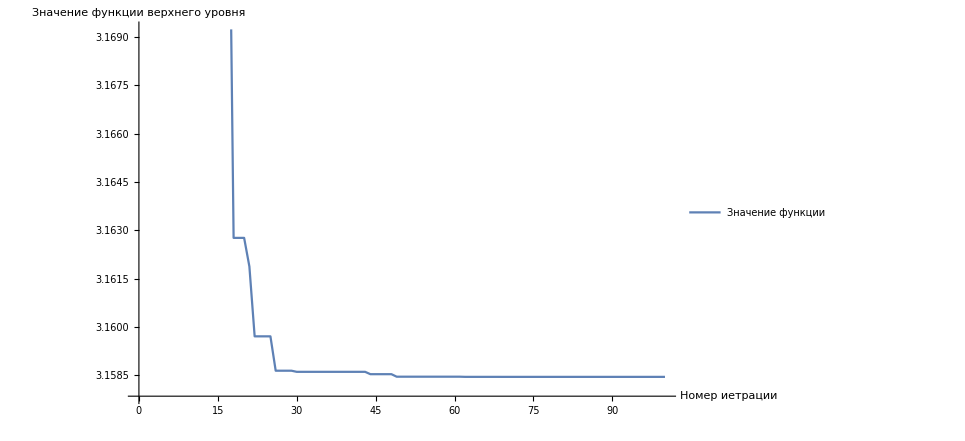

```mathematica
ListLinePlot[upperLevelFunctionValueListMin⟦;;100⟧, AxesLabel->{"Номер иетрации", "Значение функции верхнего уровня"},PlotLegends->{ "Значение функции"}]
```

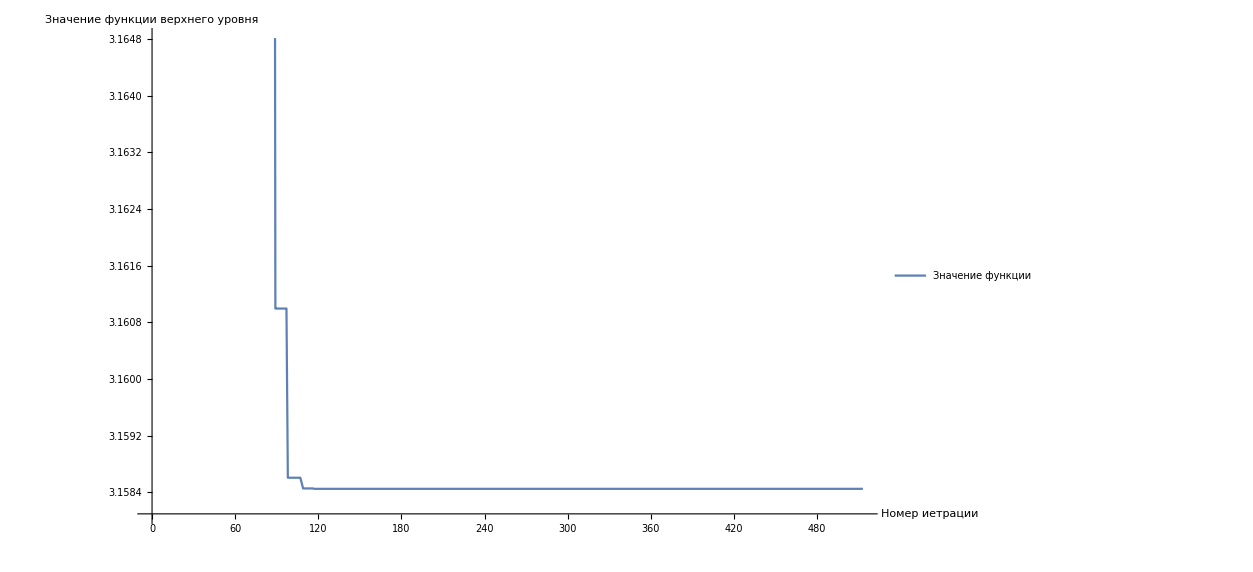

```mathematica
ListLinePlot[upperLevelFunctionValueListMax , AxesLabel->{"Номер иетрации", "Значение функции верхнего уровня"},PlotLegends->{ "Значение функции"}]
```

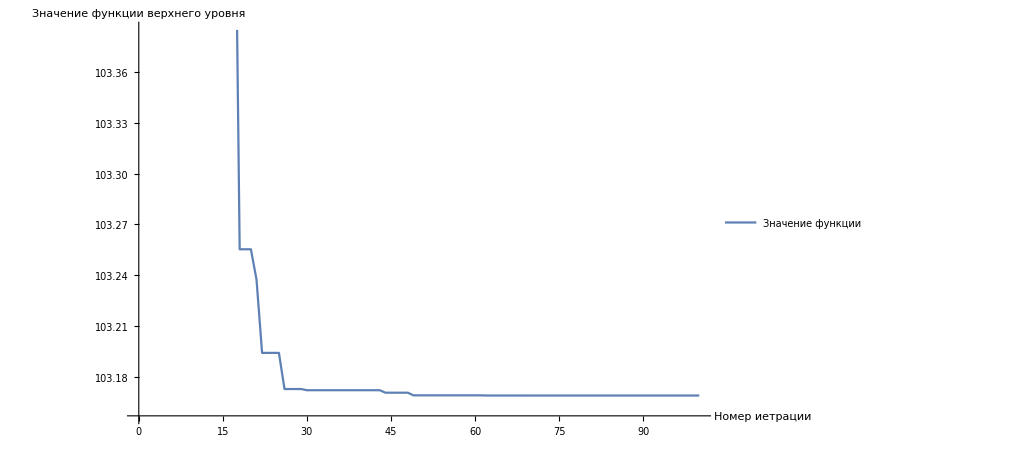

```mathematica
ListLinePlot[lowerLevelFunctionValueListMin⟦;;100⟧,  AxesLabel->{"Номер иетрации", "Значение функции верхнего уровня"},PlotLegends->{ "Значение функции"} ]
```

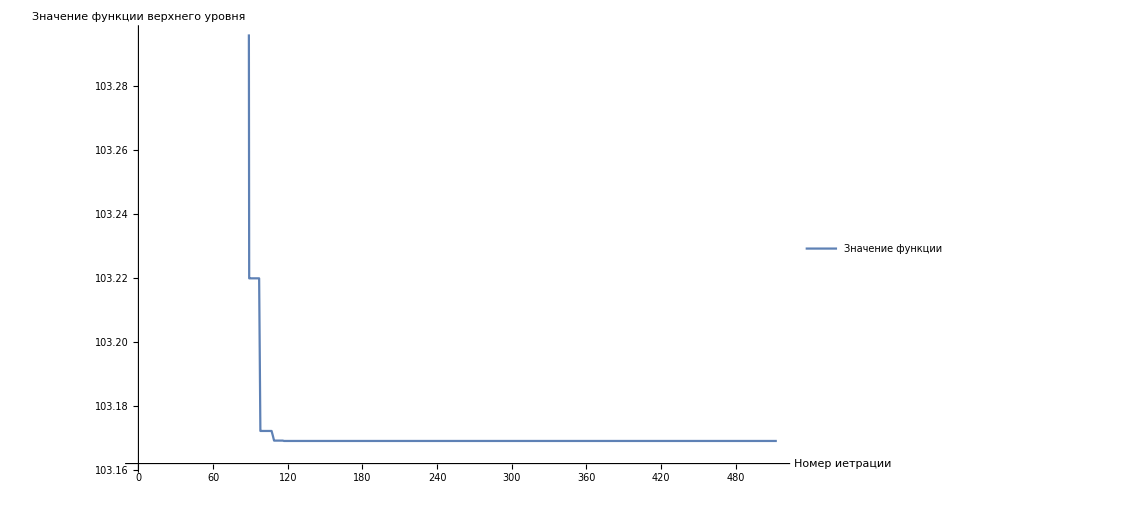

```mathematica
ListLinePlot[lowerLevelFunctionValueListMax, AxesLabel->{"Номер иетрации", "Значение функции верхнего уровня"},PlotLegends->{ "Значение функции"}]
```

```mathematica
Flatten@Import["/Users/dashavecherinka/Desktop/ВКР код/results.xlsx"]
```

{3.18873,3.18873,3.18873,3.18873,3.18873,3.18873,3.18553,3.18553,3.18553,3.17847,3.17847,3.17847,3.17847,3.17847,3.17847,3.17269,3.13483,3.13483,3.13483,3.13483,3.13483,3.13483,3.13483,3.13483,3.13483,3.13483,3.13483,3.13483,3.13483,3.13483,3.13483,3.12531,3.12531,3.12531,3.12531,3.12531,3.12531,3.12531,3.12531,3.12531,3.12531,3.12531,3.11958,3.1027,3.1027,3.1027,3.1027,3.1027,3.1027,3.1027,3.1027,3.1027,3.1027,3.1027,3.1027,3.1027,3.1027,3.1027,3.1027,3.1027,3.1027,3.1027,3.1027,3.1027,3.1027,3.1027,3.09931,3.09931,3.09931,3.09931,3.09931,3.09931,3.09931,3.09737,3.09737,3.09737,3.09737,3.09737,3.09719,3.09719,3.09719,3.09719,3.09719,3.09719,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09309,3.09215,3.09215,3.09215,3.09215,3.09215,3.09215,3.09215,3.09079,3.09079,3.09079,3.09013,3.09013,3.09013,3.09013,3.09013,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08829,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08419,3.08346,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07786,3.07742,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07528,3.07264,3.07264,3.07264,3.07264,3.07264,3.07264,3.07264,3.07264,3.07264,3.07264,3.07264,3.07264,3.07264,3.07264,3.07264,3.07264,3.07264,3.07264,3.06992,3.06992,3.06992,3.06992,3.06992,3.06992,3.06992,3.06992,3.06992,3.06992,3.06992,3.06992,3.06992,3.06992,3.06992,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06958,3.06824,3.06824,3.06824,3.06824,3.06558,3.06558,3.06558,3.06558,3.06558,3.06558,3.06558,3.06558,3.06558,3.06558,3.06558,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.0639,3.06375,3.06375,3.06375,3.06331,3.06331,3.06331,3.06331,3.06331,3.06331,3.06331,3.06331,3.06331,3.06331,3.06331,3.06331,3.06331,3.06331,3.0628,3.0628,3.0628,3.0628,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.0606,3.05966,3.05966,3.05966,3.05966,3.05966,3.05966,3.05966,3.05966,3.05966,3.05966,3.05966,3.05966,3.05966,3.05966,3.05966,3.05966,3.05966,3.05966,3.05966,3.05966,3.057,3.057,3.057,3.057,3.057,3.057,3.057,3.057,3.057,3.057,3.057,3.057,3.057,3.057,3.057,3.05462,3.05462,3.05462,3.05462,3.05462,3.05462,3.05462,3.05462,3.05462,3.05462,3.05462,3.05462,3.05462,3.05462,3.05462}

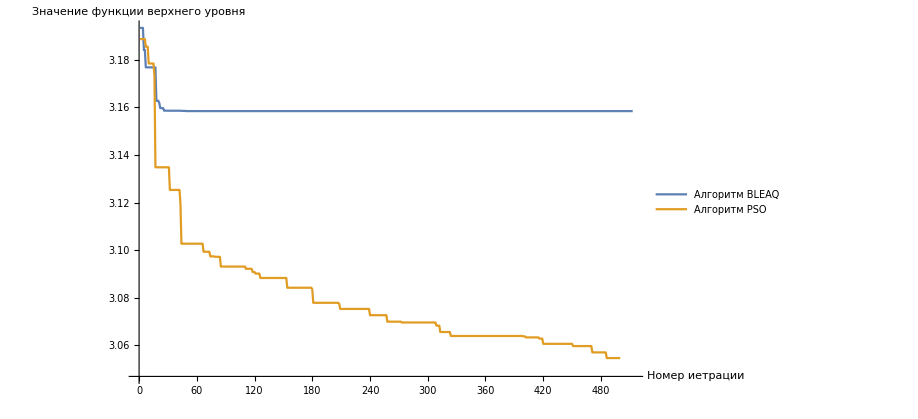

```mathematica
ListLinePlot[{upperLevelFunctionValueListMin,(Flatten@Import["/Users/dashavecherinka/Desktop/ВКР код/results.xlsx"])}, AxesLabel->{"Номер иетрации", "Значение функции верхнего уровня"},PlotLegends->{"Алгоритм BLEAQ","Алгоритм PSO"}]
```